```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A=({{0, -ⅈ}, {-ⅈ, 0}}); W[a_]:=({{Exp[a], 0}, {0, Exp[-a]}});(*Stokes, Antistokes and phase operatoes*)
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];(*From f''+af'+bf==0 to y''+Qy==0*)
U[Q_,g_,x_]:=Function[z,FullSimplify[(Q[g] D[g,x]^2-3/4(D[g,{x,2}]/D[g,x])^2+1/2(D[g,{x,3}]/D[g,x]))/.x->z]];(*From f''+Qf==0 to y''+Uy==0 with variable exchange*)
line[a_,b_]:=Function[t,a+(b-a)t];
```

```mathematica
StokesGraph[Q_,l_]:=
Module[{zeros,poles,z,x,y,i,zerosPlot,polesPlot,plotRange,stokes, antistokes},
zeros=NSolve[Q[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];
zerosPlot=ListPlot[Table[{Re[zeros⟦i⟧],Im[zeros⟦i⟧]},{i,1,Length[zeros]}],PlotStyle->Blue];

poles=NSolve[Q[z]^-1==0,z];
poles=Table[z/.poles⟦i⟧,{i,1,Length[poles]}];
polesPlot=ListPlot[Table[{Re[poles⟦i⟧],Im[poles⟦i⟧]},{i,1,Length[poles]}],PlotStyle->Red];

plotRange={{Min[Min[Re[zeros]],Min[Re[poles]]]-l,Max[Max[Re[zeros]],Max[Re[poles]]]+l},{Min[Min[Im[zeros]],Min[Im[poles]]]-l,Max[Max[Im[zeros]],Max[Im[poles]]]+l}};
stokes=StreamPlot[{Cos[-1/2 Arg[Q[x+ⅈ y]]],Sin[-1/2 Arg[Q[x+ⅈ y]]]},{x,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{y,plotRange⟦2,1⟧,plotRange⟦2,2⟧}];
antistokes=StreamPlot[{Cos[-(Arg[Q[x+ⅈ y]]+π)/2],Sin[-(Arg[Q[x+ⅈ y]]+π)/2]},{x,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{y,plotRange⟦2,1⟧,plotRange⟦2,2⟧}];
{Show[stokes,zerosPlot,polesPlot,ImageSize->Large],Show[antistokes,zerosPlot,polesPlot,ImageSize->Large]}
];
```

```mathematica
sqrt[f_,{x_,start_,a_,b_,end_}]:=
Module[{roots,chunks,cuts,i,t},
roots=NSolve[Im[f[t]]==0&&a<t<b,t]//Quiet;
cuts={start};
For[i=1,i≤Length[roots],i++,
If[Re[f[t/.roots⟦i⟧]]<0,AppendTo[cuts,t/.roots⟦i⟧],];
];
AppendTo[cuts,end];

chunks={};
For[i=2,i≤Length[cuts],i++,
AppendTo[chunks,If[Mod[i,2]==0,{√f[x],cuts⟦i-1⟧<x<cuts⟦i⟧},{-√f[x],cuts⟦i-1⟧<x<cuts⟦i⟧}]];
];

Piecewise[chunks]
];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

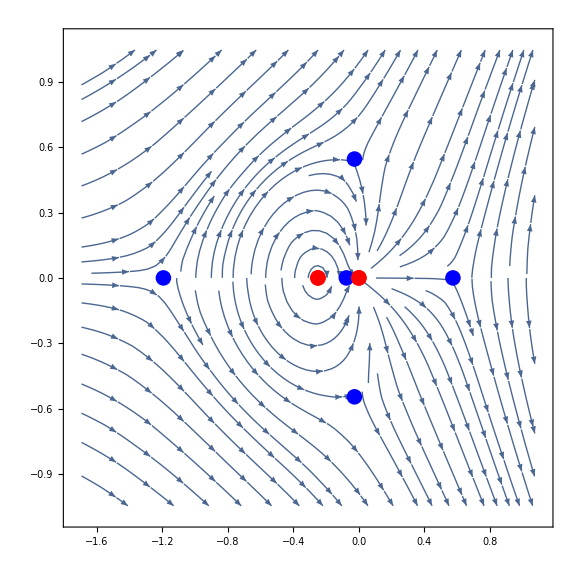
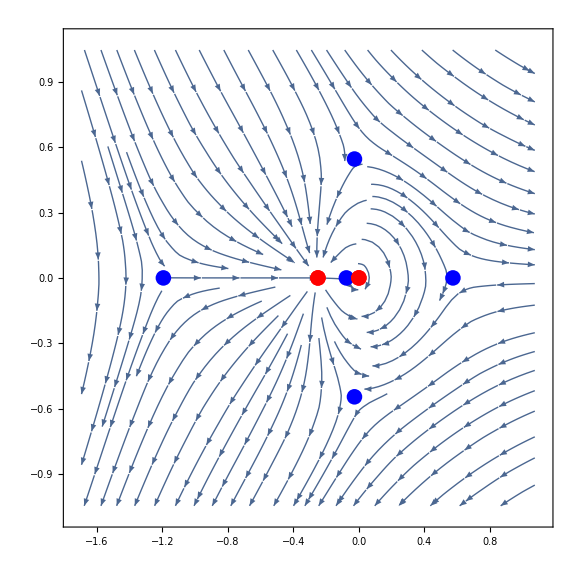

```mathematica
β=0.7;δ=0.5;
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
StokesGraph[potential,0.5]
Clear[β,δ,potential];
```

{-2.03165,-0.878183+0.87125 ⅈ,-0.878183-0.87125 ⅈ,0.431107,-0.273089}

0.263902-1.54755 ⅈ

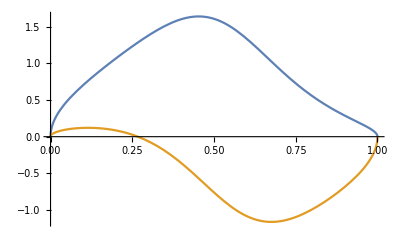
{-Graphics-,-Graphics-}

```mathematica
β=0.1;δ=1.1;
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦2⟧;
c=zeros⟦1⟧;

f=Function[t,potential[line[a,c][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-c)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,c,f,zeros,chunks,sqrtf,potential];
```

```mathematica
Dissipation={};
begining=-1;end=1;nstep=100;β=0.1;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

For[δ=begining,δ≤end,δ+=(end-begining)/nstep,
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=If[Length[zeros]>3,zeros⟦2⟧,zeros⟦1⟧];
(*b=-δ^2;*)
c=zeros⟦1⟧;

f=Function[t,potential[line[a,c][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

ac=If[a==c,0,NIntegrate[-ⅈ (a-c)sqrtf[t],{t,0,1}]];
(*bc=NIntegrate[-ⅈ (b-c)√(potential[s]/.s->line[b,c][t]),{t,0,1}];*)

R=ⅇ^(-2 (ac)) Subscript[s, 1]+ⅇ^(-2 bc) Subscript[s, 2]+Subscript[s, 3]/.{Subscript[s, 1]->ⅈ,Subscript[s, 2]->0,Subscript[s, 3]->ⅈ};
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β,a,b,c,ac,bc,zeros,f,chunks,sqrtf,potential];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.542953}. NIntegrate obtained 13.0823  - 4.54606\ ⅈ and 0.465958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.460922}. NIntegrate obtained -19.9171 + 5.84978\ ⅈ and 6.61246 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.460922}. NIntegrate obtained -16.4499 + 4.45406\ ⅈ and 4.63544 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

-Graphics-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

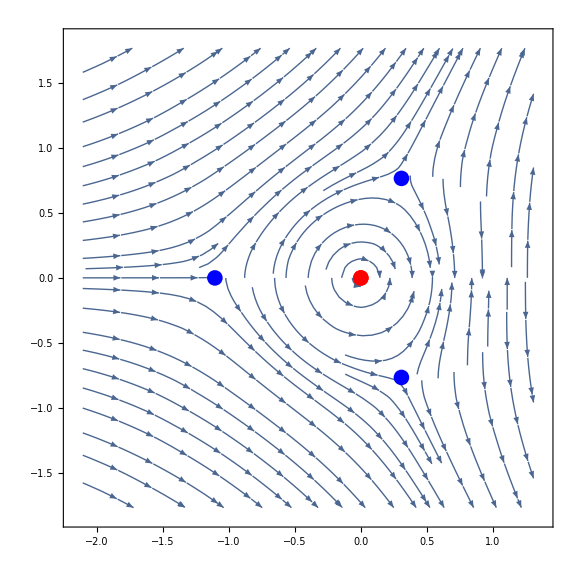
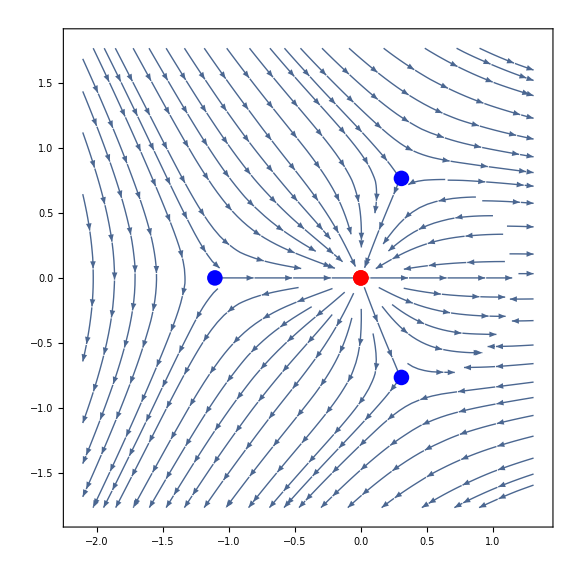

```mathematica
β=0;δ=0.7;
potential=Function[x,-(δ^2+x+3/(4 x^2))];
StokesGraph[potential,1]
Clear[β,δ,potential];
```

{-1.38883,0.194416+0.708678 ⅈ,0.194416-0.708678 ⅈ}

0.804431-1.55939 ⅈ

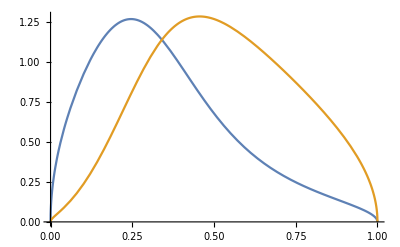
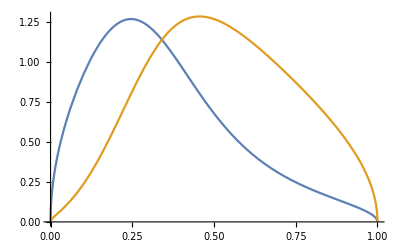

```mathematica
δ=1;
potential=Function[x,-(δ^2+x+3/(4 x^2))];
zeros=NSolve[potential[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦3⟧;
b=zeros⟦1⟧;

f=Function[t,potential[line[a,b][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-b)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,b,f,zeros,chunks,sqrtf,potential];
```

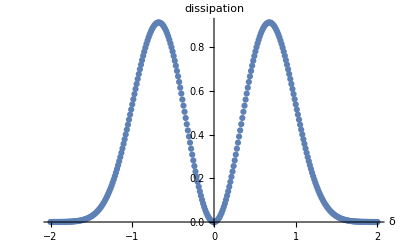

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

δ=0;
potential=Function[x,-3/(4 x^2)-x-δ^2];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=zeros⟦3⟧;
b=zeros⟦1⟧;

f=Function[t,potential[line[a,b][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

ab0=NIntegrate[-ⅈ (a-b)sqrtf[t],{t,0,1}];

For[δ=begining,δ≤end,δ+=(end-begining)/nstep,
potential=Function[x,-3/(4 x^2)-x-δ^2];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=zeros⟦3⟧;
b=zeros⟦1⟧;

f=Function[t,potential[line[a,b][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

ab=NIntegrate[-ⅈ (a-b)sqrtf[t],{t,0,1}];

R=ⅇ^(-2 ab) Subscript[s, 1]+Subscript[s, 2]/.{Subscript[s, 1]->2ⅈ ⅇ^(2ab0),Subscript[s, 2]->-ⅈ};
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,a,b,ab,ab0,f,chunks,sqrtf,potential,zeros];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"}]
```

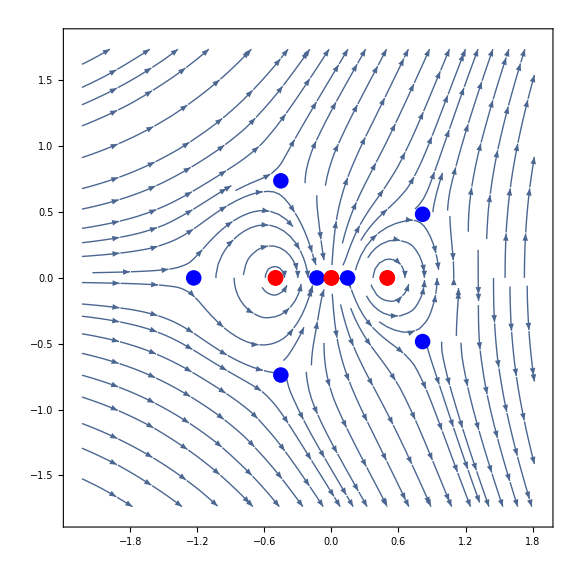
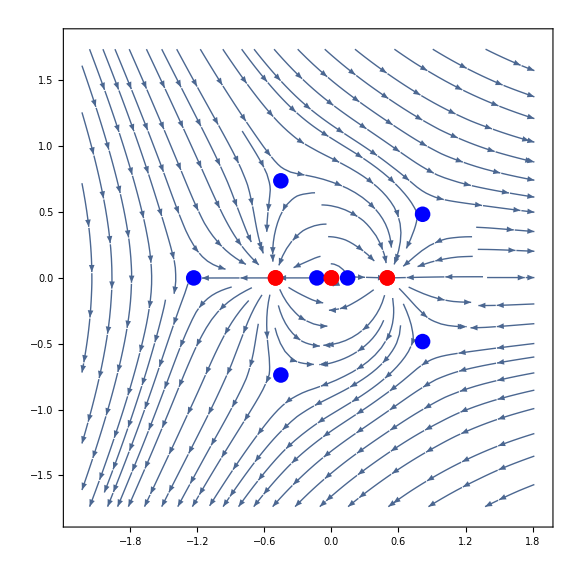

```mathematica
β=0.5;δ=0.7;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
StokesGraph[potential,1]
Clear[β,δ,potential];
```

{-1.73611,1.31554+0.4343 ⅈ,1.31554-0.4343 ⅈ,-1.02629+0.811529 ⅈ,-1.02629-0.811529 ⅈ,0.302496,-0.144892}

-0.319771-0.892839 ⅈ

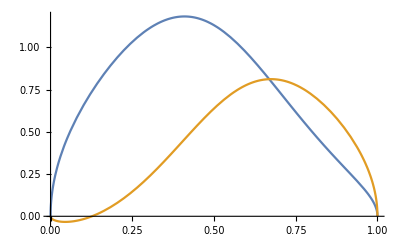
{-Graphics-,-Graphics-}

```mathematica
δ=1;β=1;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦5⟧;
c=zeros⟦1⟧;

f=Function[t,potential[line[a,c][t]]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-c)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,c,f,zeros,chunks,sqrtf,potential];
```

{-1.29452,0.821349+0.676567 ⅈ,0.821349-0.676567 ⅈ,-0.203051+0.60926 ⅈ,-0.203051-0.60926 ⅈ,0.169976,-0.152052}

0.596717+0.790222 ⅈ

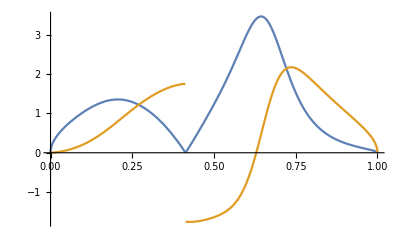
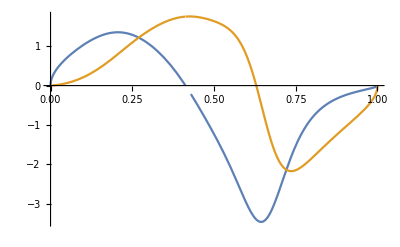

```mathematica
δ=-0.2;β=0.5;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

b=zeros⟦3⟧;
c=zeros⟦1⟧;

f=Function[t,potential[line[b,c][t]]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (b-c)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,b,c,f,zeros,chunks,sqrtf,potential];
```

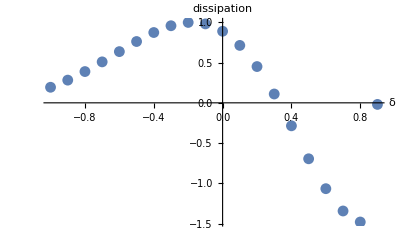

```mathematica
Dissipation={};
begining=-1;end=1;nstep=20;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
β=0.5;

For[δ=begining,δ<end,δ+=(end-begining)/nstep,
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=zeros⟦5⟧;
b=zeros⟦3⟧;
c=zeros⟦1⟧;

f=Function[t,potential[line[a,c][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtAC=Function[t,chunks];
ac=NIntegrate[-ⅈ (a-c)sqrtAC[t],{t,0,1}];

f=Function[t,potential[line[b,c][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtBC=Function[t,chunks];
bc=NIntegrate[-ⅈ (b-c)sqrtBC[t],{t,0,1}];

R=ⅇ^(-2 ac) Subscript[s, 1]+ⅇ^(-2 bc) Subscript[s, 2]+Subscript[s, 3]/.{Subscript[s, 1]->-ⅈ,Subscript[s, 2]->0,Subscript[s, 3]->-ⅈ};
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β,a,b,c,ac,bc,sqrtAC,sqrtBC,f,chunks,potential,zeros];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"}]
```